```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

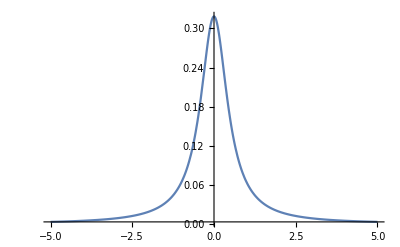

```mathematica
Plot[(1/Pi)/(1+(4 x^2)),{x,-5,5}, PlotRange->Full,FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}}]
```

```mathematica
cadena = Subscript[δ,n] "(t)"
```

(t) δ_n

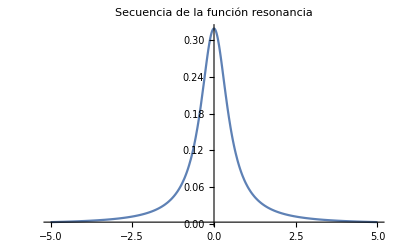

```mathematica
Plot[1/(π(1+4 x^2)),{x,-5,5},PlotTheme->"Minimal",PlotRange->Full,FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}},PlotLabel->"Secuencia de la función resonancia",LabelStyle->Directive[Black, FontSize->14]]
```

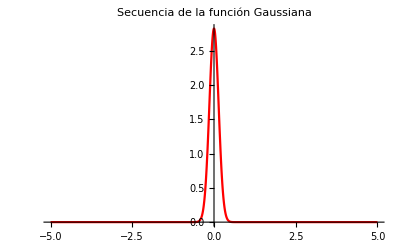

```mathematica
Plot[(5 Exp[-25 x^2])/Sqrt[π],{x,-5,5},PlotTheme->"Minimal",PlotRange->Full,FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}},PlotLabel->"Secuencia de la función Gaussiana", PlotStyle->{Red},  LabelStyle->Directive[Black,FontSize->14]]
```

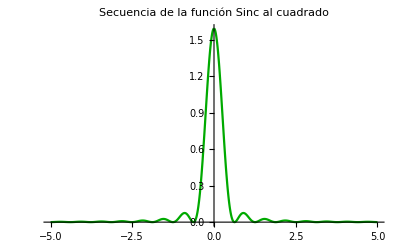

```mathematica
Plot[(Sin[5 x])^2/(5 π x^2),{x,-5,5},PlotTheme->"Minimal",PlotRange->Full,FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}},PlotLabel->"Secuencia de la función Sinc al cuadrado",PlotStyle->{Darker[Green]},  LabelStyle->Directive[Black, FontSize->14]]
```

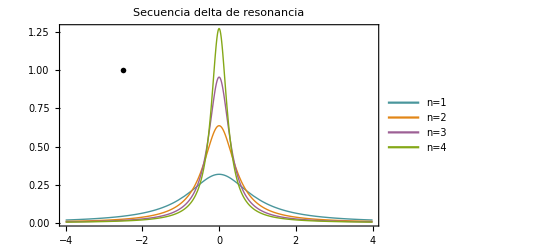

```mathematica
f[n_, x_]:=(n/Pi)/(1+n^2 x^2);
(*cadena1="δ (t)=(n/π)/(1 + SuperscriptBox[n, 2]SuperscriptBox[t, 2])";*)
cadena1=MaTeX["\\delta (t) = \\frac{n/\\pi}{(1 +n^2 t^2)}",FontSize->14];
Plot[Table[f[n,x],{n,1,4}]//Evaluate,{x,-4,4},Frame->True,PlotRange->All,PlotStyle->98,Method->"DefaultPlotStyle"-> Thick, PlotLegends->Table["n="<>ToString[n],{n,1,4}],PlotLabel->Style["Secuencia delta de resonancia",Black,16], Epilog->Text[cadena1,{-2.5,1}]]
```

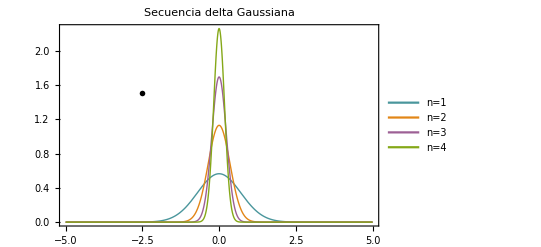

```mathematica
g[n_,x_]:= (n Exp[-n^2 x^2])/Sqrt[π];
(*cadena2="δ (t)=(n SuperscriptBox[e, -SuperscriptBox[n, 2] SuperscriptBox[x, 2]])/(√π)";*)
cadena2=MaTeX["\\delta (t)=\\frac{n e^{-n^2 t^2}}{\\sqrt{\\pi}}", FontSize->14];
Plot[Table[g[n,x],{n,1,4}]//Evaluate,{x,-5,5},Frame->True,PlotRange->All,PlotStyle->98,Method->"DefaultPlotStyle"-> Thick, PlotLegends->Table["n="<>ToString[n],{n,1,4}],PlotLabel->Style["Secuencia delta Gaussiana",Black,16], Epilog->Text[cadena2,{-2.5,1.5}]]
```

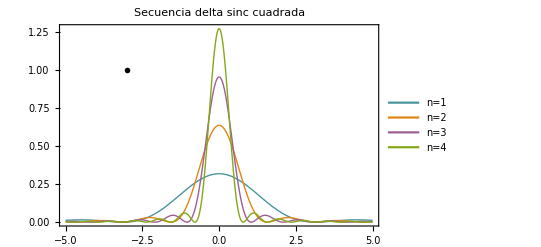

```mathematica
h[n_,x_]:= (Sin[n x])^2/(n π x^2);
(*cadena3="δ (t)=sin^2/(n π SuperscriptBox[t, 2])";*)
cadena3 = MaTeX["\\delta (t) = \\frac{\\sin^2 n t}{n \\pi t^2}",FontSize->14];
Plot[Table[h[n,x],{n,1,4}]//Evaluate,{x,-5,5},Frame->True,PlotRange->All,PlotStyle->98,Method->"DefaultPlotStyle"-> Thick, PlotLegends->Table["n="<>ToString[n],{n,1,4}],PlotLabel->Style["Secuencia delta sinc cuadrada",Black,16], Epilog->Text[cadena3,{-3,1}]]
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
MaTeX["\\sum_{k=1}^{\\infty} \\frac{1}{k^2} = \\frac{\\pi^2}{6}",FontSize->24]
```

-Graphics-

```mathematica
MaTeX["\\delta (t) = \\frac{\\sin^2 n t}{n \\pi t^2}",FontSize->24]
```

-Graphics-

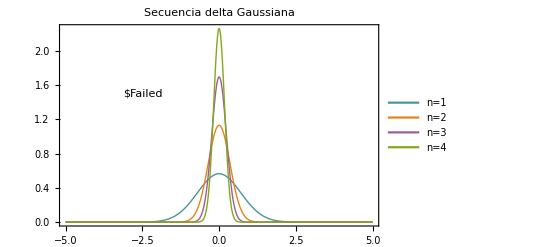

```mathematica
g[n_,x_]:= (n Exp[-n^2 x^2])/Sqrt[π];
(*cadena2="δ (t)=(n SuperscriptBox[e, -SuperscriptBox[n, 2] SuperscriptBox[x, 2]])/(√π)";*)
cadena2=MaTeX["\\delta (t)=\\frac{n e^-n^2 t^2{\\sqrt{\\pi}}", FontSize->14];
Plot[Table[g[n,x],{n,1,4}]//Evaluate,{x,-5,5},Frame->True,PlotRange->All,PlotStyle->98,Method->"DefaultPlotStyle"-> Thick, PlotLegends->Table["n="<>ToString[n],{n,1,4}],PlotLabel->Style["Secuencia delta Gaussiana",Black,16], Epilog->Text[cadena2,{-2.5,1.5}]]
```

```mathematica
MaTeX["\\delta (t)=\\frac{n e^{-n^2 t^2}}{\\sqrt{\\pi}}", FontSize->14]
```

-Graphics-